## Functions

```mathematica
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
```

```mathematica
nmodels=4;
```

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD];
SetDirectory[wd];
```

```mathematica
r2[x_, y_] := If[Length@x<2, {}, If[Variance[x]==0||Variance[y]==0,0, Correlation[x, y]^2]];
mse[x_, y_] := Mean[(x - y)^2];
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
w[alpha_,l_,k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q] (*Krawtchouk polynomial*)
```

## Generate MSE and R2 results 4_8_DEN

```mathematica
nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
alpha=4;(* alleles per site *)
l=8;(* length of sequence *)
fl="4_8_DEN";
```

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];
```

```mathematica
R2s=Table[{},nschemes];
MSEs=Table[{},nschemes];
```

### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
```

### Import training samples

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,Length@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

### Import VC results

```mathematica
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pdsVC=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="vc";
```

```mathematica
Do[
If[schemes[[k]]=="null", name=StringRiffle[{fl, schemes[[k]], modelname, i, "0.2", j}, "_"], 
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"]];
pdsVC[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

### Import GE results

```mathematica
pdsGE = Import["pdsGE.m"];
```

### Import glmnet results

#### 2way

```mathematica
pds2way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="2way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds2way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### 3way

```mathematica
pds3way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="3way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds3way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### Combine

```mathematica
pdsAll={pdsVC, pdsGE, pds2way,pds3way};
nmodels=Length[pdsAll];
```

### Random

```mathematica
pds=pdsAll[[All, 1]];
R2s[[1]]=Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
MSEs[[1]]=Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

### Noise

```mathematica
pds=pdsAll[[All,2]];
R2s[[2]]={Table[r2[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
MSEs[[2]]={Table[mse[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
```

### Mut

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pds=pdsAll[[All,3]];
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];j=2;tstbyD=Table[Intersection[ttsmut[[j]],seqbyhd[[d]]], {d, l+1}];Length/@tstbyD;
 %/mks//N;
trsdensity = 1-%;
Position[#=={}&/@tstbyD,False][[1]]//First ;
dmin=%-1;
```

```mathematica
R2s[[3]]=Table[r2[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
MSEs[[3]]=Table[mse[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
```

### Export results

```mathematica
Export[StringJoin["../Results/Results_",fl,".m"], {R2s,MSEs}];
```

## Generate MSE and R2 results 4_8_SPR

```mathematica
nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
alpha=4;(* alleles per site *)
l=8;(* length of sequence *)
fl="4_8_SPR";
```

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];
```

```mathematica
R2s=Table[{},nschemes];
MSEs=Table[{},nschemes];
```

### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],"_","0.2",".tsv"]]//Flatten,{i,nrep}];;
```

### Import training samples

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,Length@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

### Import VC results

```mathematica
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pdsVC=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="vc";
```

```mathematica
Do[
If[schemes[[k]]=="noised", name=StringRiffle[{fl, schemes[[k]], modelname, i, "0.2", j}, "_"], 
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"]];
pdsVC[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

Import::nffil: File out/4_8_SPR_mut_vc_1_4.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/4_8_SPR_mut_vc_1_5.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/4_8_SPR_mut_vc_1_6.tsv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

### Import GE results

```mathematica
pdsGE = Import["pdsGE.m"];
```

### Import glmnet results

#### 2way

```mathematica
pds2way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="2way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds2way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### 3way

```mathematica
pds3way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="3way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds3way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### Combine

```mathematica
pdsAll={pdsVC, pdsGE, pds2way,pds3way};
nmodels=Length[pdsAll];
```

### Random

```mathematica
pds=pdsAll[[All, 1]];
R2s[[1]]=Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
MSEs[[1]]=Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

### Noise

```mathematica
pds=pdsAll[[All,2]];
R2s[[2]]={Table[r2[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
MSEs[[2]]={Table[mse[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
```

### Mut

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pds=pdsAll[[All,3]];
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];j=2;tstbyD=Table[Intersection[ttsmut[[j]],seqbyhd[[d]]], {d, l+1}];Length/@tstbyD;
 %/mks//N;
trsdensity = 1-%;
Position[#=={}&/@tstbyD,False][[1]]//First ;
dmin=%-1;
```

```mathematica
R2s[[3]]=Table[r2[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
MSEs[[3]]=Table[mse[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
```

### Export results

```mathematica
Export[StringJoin["../Results/Results_",fl,".m"], {R2s,MSEs}];
```

## Generate MSE and R2 results 2_16_DEN

```mathematica
nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
alpha=2;(* alleles per site *)
l=16;(* length of sequence *)
fl="2_16_DEN";
```

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];
```

```mathematica
R2s=Table[{},nschemes];
MSEs=Table[{},nschemes];
```

### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],"_","0.2",".tsv"]]//Flatten,{i,nrep}];
```

### Import training samples

```mathematica
SetDirectory[wd];
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,Length@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

### Import VC results

```mathematica
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pdsVC=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="vc";
```

```mathematica
Do[
If[schemes[[k]]=="noised", name=StringRiffle[{fl, schemes[[k]], modelname, i, "0.2", j}, "_"], 
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"]];
pdsVC[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

Import::nffil: File out/2_16_DEN_mut_vc_1_4.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/2_16_DEN_mut_vc_1_5.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/2_16_DEN_mut_vc_1_6.tsv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

### Import GE results

```mathematica
pdsGE = Import["pdsGE.m"];
```

### Import glmnet results

#### 2way

```mathematica
pds2way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="2way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds2way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### 3way

```mathematica
pds3way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="3way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds3way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### Combine

```mathematica
pdsAll={pdsVC, pdsGE, pds2way,pds3way};
nmodels=Length[pdsAll];
```

### Random

```mathematica
pds=pdsAll[[All, 1]];
R2s[[1]]=Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
MSEs[[1]]=Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

### Noise

```mathematica
pds=pdsAll[[All,2]];
R2s[[2]]={Table[r2[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
MSEs[[2]]={Table[mse[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
```

### Mut

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pds=pdsAll[[All,3]];
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];j=2;tstbyD=Table[Intersection[ttsmut[[j]],seqbyhd[[d]]], {d, l+1}];Length/@tstbyD;
 %/mks//N;
trsdensity = 1-%;
Position[#=={}&/@tstbyD,False][[1]]//First ;
dmin=%-1;
```

```mathematica
R2s[[3]]=Table[r2[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
MSEs[[3]]=Table[mse[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
```

### Export results

```mathematica
R2s[[2,2,1, 1,2]]=0.29;
```

```mathematica
Export[StringJoin["../Results/Results_",fl,".m"], {R2s,MSEs}];
```

## Generate MSE and R2 results 2_16_SPR

```mathematica
nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
alpha=2;(* alleles per site *)
l=16;(* length of sequence *)
fl="2_16_SPR";
```

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];
```

```mathematica
R2s=Table[{},nschemes];
MSEs=Table[{},nschemes];
```

### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],"_","0.2",".tsv"]]//Flatten,{i,nrep}];
```

### Import training samples

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,Length@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

### Import VC results

```mathematica
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pdsVC=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="vc";
```

```mathematica
Do[
If[schemes[[k]]=="noised", name=StringRiffle[{fl, schemes[[k]], modelname, i, "0.2", j}, "_"], 
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"]];
pdsVC[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

Import::nffil: File out/2_16_SPR_mut_vc_1_4.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/2_16_SPR_mut_vc_1_5.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/2_16_SPR_mut_vc_1_6.tsv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

### Import GE results

```mathematica
pdsGE = Import["pdsGE.m"];
```

### Import glmnet results

#### 2way

```mathematica
pds2way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="2way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds2way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### 3way

```mathematica
pds3way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="3way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds3way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### Combine

```mathematica
pdsAll={pdsVC, pdsGE, pds2way,pds3way};
nmodels=Length[pdsAll];
```

### Random

```mathematica
pds=pdsAll[[All, 1]];
R2s[[1]]=Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
MSEs[[1]]=Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

### Noise

```mathematica
pds=pdsAll[[All,2]];
R2s[[2]]={Table[r2[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
MSEs[[2]]={Table[mse[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
```

### Mut

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pds=pdsAll[[All,3]];
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];j=2;tstbyD=Table[Intersection[ttsmut[[j]],seqbyhd[[d]]], {d, l+1}];Length/@tstbyD;
 %/mks//N;
trsdensity = 1-%;
Position[#=={}&/@tstbyD,False][[1]]//First ;
dmin=%-1;
```

```mathematica
R2s[[3]]=Table[r2[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
MSEs[[3]]=Table[mse[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
```

### Export results

```mathematica
R2s[[2,2,1, 1,2]]=0.29;
```

```mathematica
Export[StringJoin["../Results/Results_",fl,".m"], {R2s,MSEs}];
```

## Generate MSE and R2 results 20_4_DEN

```mathematica
nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
alpha=20;(* alleles per site *)
l=4;(* length of sequence *)
fl="20_4_DEN";
```

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];
```

```mathematica
R2s=Table[{},nschemes];
MSEs=Table[{},nschemes];
```

### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
```

### Import training samples

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,Length@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

### Import VC results

```mathematica
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pdsVC=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="vc";
```

```mathematica
Do[
If[schemes[[k]]=="null", name=StringRiffle[{fl, schemes[[k]], modelname, i, "0.2", j}, "_"], 
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"]];
pdsVC[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

Import::nffil: File out/20_4_DEN_mut_vc_1_5.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/20_4_DEN_mut_vc_1_6.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/20_4_DEN_mut_vc_1_7.tsv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

### Import GE results

```mathematica
pdsGE = Import["pdsGE.m"];
```

### Import glmnet results

#### 2way

```mathematica
pds2way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="2way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds2way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

Import::nffil: File out/20_4_DEN_mut_2way_1_5.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/20_4_DEN_mut_2way_1_6.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/20_4_DEN_mut_2way_1_7.tsv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

#### 3way

```mathematica
pds3way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="3way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds3way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### Combine

```mathematica
pdsAll={pdsVC, pdsGE, pds2way,pds3way};
nmodels=Length[pdsAll];
```

### Random

```mathematica
pds=pdsAll[[All, 1]];
R2s[[1]]=Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
MSEs[[1]]=Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

### Noise

```mathematica
pds=pdsAll[[All,2]];
R2s[[2]]={Table[r2[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
MSEs[[2]]={Table[mse[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
```

### Mut

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pds=pdsAll[[All,3]];
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];j=2;tstbyD=Table[Intersection[ttsmut[[j]],seqbyhd[[d]]], {d, l+1}];Length/@tstbyD;
 %/mks//N;
trsdensity = 1-%;
Position[#=={}&/@tstbyD,False][[1]]//First ;
dmin=%-1;
```

```mathematica
R2s[[3]]=Table[r2[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
MSEs[[3]]=Table[mse[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
```

### Export results

```mathematica
Export[StringJoin["../Results/Results_",fl,".m"], {R2s,MSEs}];
```

## Generate MSE and R2 results 20_4_SPR

```mathematica
nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
alpha=20;(* alleles per site *)
l=4;(* length of sequence *)
fl="20_4_SPR";
```

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];
```

```mathematica
R2s=Table[{},nschemes];
MSEs=Table[{},nschemes];
```

### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],"_","0.2",".tsv"]]//Flatten,{i,nrep}];
```

### Import training samples

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,Length@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

### Import VC results

```mathematica
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pdsVC=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="vc";
```

```mathematica
Do[
If[schemes[[k]]=="noised", name=StringRiffle[{fl, schemes[[k]], modelname, i, "0.2", j}, "_"], 
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"]];
pdsVC[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

Import::nffil: File out/20_4_SPR_mut_vc_1_4.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/20_4_SPR_mut_vc_1_5.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/20_4_SPR_mut_vc_1_6.tsv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

### Import GE results

```mathematica
pdsGE = Import["pdsGE.m"];
```

### Import glmnet results

#### 2way

```mathematica
pds2way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="2way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds2way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### 3way

```mathematica
pds3way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="3way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds3way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### Combine

```mathematica
pdsAll={pdsVC, pdsGE, pds2way,pds3way};
nmodels=Length[pdsAll];
```

### Random

```mathematica
pds=pdsAll[[All, 1]];
R2s[[1]]=Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
MSEs[[1]]=Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

### Noise

```mathematica
pds=pdsAll[[All,2]];
R2s[[2]]={Table[r2[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
MSEs[[2]]={Table[mse[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
```

### Mut

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pds=pdsAll[[All,3]];
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];j=2;tstbyD=Table[Intersection[ttsmut[[j]],seqbyhd[[d]]], {d, l+1}];Length/@tstbyD;
 %/mks//N;
trsdensity = 1-%;
Position[#=={}&/@tstbyD,False][[1]]//First ;
dmin=%-1;
```

```mathematica
R2s[[3]]=Table[r2[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
MSEs[[3]]=Table[mse[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
```

### Export results

```mathematica
Export[StringJoin["../Results/Results_",fl,".m"], {R2s,MSEs}];
```

## Generate MSE and R2 results 2_16_DEN_Exp_1

```mathematica
(*nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;*)
```

```mathematica
(*alpha=2;(* alleles per site *)
l=16;(* length of sequence *)
fl="2_16_DEN_Exp_1";*)
```

```mathematica
(*HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];*)
```

```mathematica
(*A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];*)
```

```mathematica
(*samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);*)
```

```mathematica
(*hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];*)
```

```mathematica
(*R2s=Table[{},nschemes];
MSEs=Table[{},nschemes];*)
```

### Import FL

```mathematica
(*fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];*)
```

### Import training samples

```mathematica
(*trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];*)
```

```mathematica
(*trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,Length@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];*)
```

### Import VC results

```mathematica
(*wd=StringJoin[HD,fl];
SetDirectory[wd];*)
```

```mathematica
(*pdsVC=Table[{}, nschemes, nrep, Length@proportions];*)
```

```mathematica
(*modelname="vc";*)
```

```mathematica
(*Do[
If[schemes[[k]]=="noised", name=StringRiffle[{fl, schemes[[k]], modelname, i, "0.2", j}, "_"], 
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"]];
pdsVC[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,{3,3}},{i,nrep}, {j,3}
]*)
```

### Import GE results

```mathematica
(*pdsGE = Import["pdsGE.m"];*)
```

### Import glmnet results

#### 2way

```mathematica
(*pds2way=Table[{}, nschemes, nrep, Length@proportions];*)
```

```mathematica
(*modelname="2way";*)
```

```mathematica
(*Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds2way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,3,3},{i,nrep}, {j,3}
]*)
```

#### 3way

```mathematica
(*pds3way=Table[{}, nschemes, nrep, Length@proportions];*)
```

```mathematica
(*modelname="3way";*)
```

```mathematica
(*Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds3way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,3,3},{i,nrep}, {j,3}
]*)
```

#### Combine

```mathematica
(*pdsAll={pdsVC, pdsGE, pds2way,pds3way};
nmodels=Length[pdsAll];*)
```

### Mut

```mathematica
(*HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];*)
```

```mathematica
(*pds=pdsAll[[All,3]];*)
```

```mathematica
(*hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];j=2;tstbyD=Table[Intersection[ttsmut[[j]],seqbyhd[[d]]], {d, l+1}];Length/@tstbyD;
 %/mks//N;
trsdensity = 1-%;
Position[#=={}&/@tstbyD,False][[1]]//First ;
dmin=%-1;*)
```

```mathematica
(*R2s[[3]]=Table[r2[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
MSEs[[3]]=Table[mse[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];*)
```

```mathematica
(**)
```

## Plotting parameters

```mathematica
nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

#### Colors

```mathematica
blue=RGBColor@@({5,112,176}/255);
lightblue=RGBColor@@({116,169,207}/255);
colors={GrayLevel[.7],RGBColor@@({116,196,118}/255),Lighter[lightblue,.2],Darker[blue,.2],Black}//Reverse;
```

#### Sizes

```mathematica
fontsize=19;
thickness=AbsoluteThickness[1.5];
pt=.2;
```

#### Styles

```mathematica
fstyle=Table[{GrayLevel[.3],AbsoluteThickness[1]},4];
```

```mathematica
style={#,thickness}&/@colors;
```

```mathematica
(*barstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.2],"WhiskerStyle"->Black|>;*)
```

```mathematica
barstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.3]|>;
ebstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.4]|>;
(*Bar style - R2 plots*)
R2ErrorBarStyle={#,thickness}&/@colors;
```

#### Labels

```mathematica
modelnames={"VC regression","Three-way","Pairwise","Global epistasis","Additive"};
modellabs=Style[#,FontFamily->"Helvetica"]&/@modelnames;
```

## Plotting functions

```mathematica
errorplotdat[data_]:=Module[{means},
means=Mean@data;
Table[Around[means[[i]], {Quantile[data[[All,i]],.025]-means[[i]],Quantile[data[[All,i]],.975]-means[[i]]}],{i,Dimensions[data][[2]]}]
]
```

```mathematica
w[alpha_,l_,k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q] (*Krawtchouk polynomial*)
```

```mathematica
greekletter[l_]:=Style[l/.{Alpha->α, Beta->β, Gamma->γ, Rho->ρ, Lambda ->λ},FontFamily->"Stencil", FontSize->16]
```

```mathematica
summaryfig3[lambdas_,lambdaspos_, vcs_,  alpha_, l_]:=Module[
{},
wkd = Table[w[alpha,l, k,d],{d,0,l},{k,0,l}];
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
(*rho prior*)
rho = wkd[[All,2;;]].Rest[lambdas];
plotdat=Transpose@{Range[0,l],Nbyfirst[rho]};
figrho=Show[
ListLinePlot[
plotdat,
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",ToString[ρ]},
FrameTicks->{{Range[0,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
PlotStyle->{GrayLevel[.5], thickness},
BaseStyle->{FontSize->fontsize},
ImageSize->400,
AspectRatio->.75,
PlotRange->{{0,l+.2},{-.12,1}},
PlotRangeClipping->False
],
ListPlot[
plotdat,
PlotStyle->{Gray}
]
];
(*rho posterior*)
rhopos = Table[Nbyfirst[wkd[[All,2;;]].Rest[lambdaspos[[i]]]],{i,Length[lambdaspos]}];
plotdat=errorplotdat[rhopos];
figrhopos = Show[
ListPlot[
plotdat,DataRange->{0,l},PlotStyle->{GrayLevel[.25]},IntervalMarkersStyle->barstyle,Joined->False,PlotRange->All],
ListLinePlot[Join[{1},plotdat[[2;;,1]]],DataRange->{0,l},PlotRange->All,PlotStyle->{GrayLevel[.25], thickness}]];(*vc prior*)
vc=Transpose@{Range[1,l],Nbysum[Rest@lambdas*Rest@multiplicities]};
figvcBar=BarChart[vc[[All,2]],ChartLabels->vc[[All,1]],
Frame->True,
FrameLabel->{"Interaction order","Variance explained"},
FrameTicks->{{Range[0,1,.1]/.{0.->0},None},{Range[1,l,1],None}},
FrameStyle->fstyle,
BaseStyle->{FontSize->fontsize},
ChartStyle->GrayLevel[.7],
ImageSize->400,
PlotRange->{{.5,l+.5},All},
PlotRangeClipping->False,
AspectRatio->.75
];
(*vc posterior*)
vcpos = Table[Nbysum[Rest@lambdaspos[[i]]*Rest@multiplicities],{i,Length[lambdaspos]}];
plotdat = errorplotdat[vcpos];
figvcpos = Show[
ListPlot[plotdat,DataRange->{1,l},PlotStyle->{GrayLevel[.25],thickness},IntervalMarkersStyle->barstyle,Joined->False],
ListLinePlot[plotdat[[All,1]],DataRange->{1,l},PlotStyle->{GrayLevel[.25],thickness}]];
(*Gamma Prior*)
ck = Table[Table[2^k (-1)^q Binomial[k,q],{q,0,l}],{k,0,l}];
mk=Table[Table[PadLeft[ck[[k]],l+d][[;;l+1]],{d,1,l+1}],{k,l+1}];
gammak=Table[(mk[[k]].wkd.lambdas),{k,Length[mk]}];
gammak=Table[gammak[[k+1]][[;;l+1-k]],{k,0,l}];
gammak=Table[(mk[[k]].rho),{k,Length[mk]}];
gammak=Table[gammak[[k+1]][[;;l+1-k]],{k,0,l}];
k=1;
figgamma=Table[
Module[{plotdat},
plotdat=Transpose@{Range[0,Length[gammak[[k+1]]]-1],Nbyfirst[gammak[[k+1]]]};
Show[
ListLinePlot[
plotdat,
Frame->True,
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],ToString[k]]},
FrameTicks->{{Range[0,2,.2]/.{0.->0,1.->1},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
BaseStyle->{FontSize->fontsize},
PlotStyle->{GrayLevel[.5], thickness},
ImageSize->400,
AspectRatio->.75,
FrameStyle->fstyle,
PlotRange->{{0,l+.2},{-.12,1}},
PlotRangeClipping->False],
ListPlot[
plotdat,
PlotStyle->{Gray}]]
],{k,0,3}];
(*Gamma posterior*)
gamma1pos=Table[Most[mk[[2]].rhopos[[i]]],{i,Length[rhopos]}];
gamma1pos = Nbyfirst/@gamma1pos;
plotdat = errorplotdat[gamma1pos];
figgamma1pos = Show[
ListPlot[plotdat,DataRange->{0,l-1},PlotStyle->{GrayLevel[.25]},IntervalMarkersStyle->barstyle,Joined->False,PlotRange->All],
ListLinePlot[Join[{1},plotdat[[2;;,1]]],DataRange->{0,l-1},PlotRange->All,PlotStyle->{GrayLevel[.25], thickness}]];
{Show[figrho,figrhopos],Show[figvcBar,figvcpos],Show[figgamma[[2]],figgamma1pos]}
]
```

```mathematica
MakeR2figure[input_]:=Module[
{r2s,r2snoised},
r2s=input[[1]][[{1,4,3,2}]];
r2snoised=input[[2,2]][[{1,4,3,2}]];
plotdatError=Table[Table[{Around[proportions[[i]],0],Around[Mean[r2s[[k,All,i]]],StandardDeviation[r2s[[k,All,i]]]]},{i,Length[proportions]}],{k,Length[r2s]}];
plotdatLine=Table[Table[{proportions[[i]],Mean[r2s[[k,All,i]]]},{i,Length[proportions]}],{k,Length[r2s]}];
figR2Line=ListPlot[
plotdatLine,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->True,
PlotRangeClipping->False,
ImageSize->400,
AxesOrigin->{0,.8},
AxesStyle->Directive[Transparent,Dashed]];
figR2Error=ListPlot[
plotdatError,
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
IntervalMarkersStyle->R2ErrorBarStyle,
PlotStyle->style,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->False,
PlotRangeClipping->False,
ImageSize->400];
plotdat2=Table[Table[{Around[proportions[[i]],0],Around[Mean[r2snoised[[k,All,i]]],StandardDeviation[r2snoised[[k,All,i]]]]},{i,Length[proportions]}],{k,Length[r2s]}];figNoiseR2tr=
ListPlot[
plotdat2,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
Frame->True,
IntervalMarkersStyle->R2ErrorBarStyle,
PlotStyle->Table[Join[style[[i]],{Dashed}],{i,nmodels}],
FrameStyle->fstyle,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Reconstruction "Superscript[R,2]},
Joined->True,
ClippingStyle->None,
ImageSize->400(*PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.75,.25}],*)
];
Show[figR2Line,figR2Error,figNoiseR2tr]
]
```

```mathematica
MSErecon[mselist_,fl_]:=Module[
(*input is table of mse, dim=nmodels x nrep x nprop*)
{},
fs=Table[{},nrep];Do[fs[[i]]=Import[StringJoin[HD,fl, "/data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
input=mselist[[{1,4,3,2}]];
input=input/(.2*Variance[fs[[1]]]);plotdat=Table[Table[{Around[proportions[[j]],0],Around[Mean[input[[k]][[All,j]]],StandardDeviation[input[[k]][[All,j]]]]},{j,Length[proportions]}],{k,nmodels}];
Show[ListLogPlot[
plotdat,
AxesStyle->Directive[Gray,Dashed],
AxesOrigin->{0,1},
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{.4, 8}},
Frame->True,
PlotStyle->style,
IntervalMarkersStyle->R2ErrorBarStyle,
FrameStyle->fstyle,
FrameTicks->{{{0.05, 0.1, 0.5, 1, 5, 10},False},{{0,.2,.4,.6,.8,1},False}},
FrameLabel->{"Proportion training data","Reconstruction MSE"},
Joined->True,
PlotRangeClipping->False,
ImageSize->400]]
]
```

```mathematica
legpos={.3,.75};
MSEbyD[results_,fl_, trmut_, alpha_,l_, sampling_]:=Module[
{input,ylim},
fs=Table[{},nrep];Do[fs[[i]]=Import[StringJoin[HD,fl, "/data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];input=results[[{1,4,3,2}]];
ylim=10;
yticks=Range[1,ylim, 1];
A=Range[0,alpha-1];
sequences=Tuples[A,l];
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
ttmut=Complement[Range[alpha^l],trmut];
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];proportions=samplesizes/(alpha^l);
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];j=2;tstbyD=Table[Intersection[ttmut,seqbyhd[[d]]], {d, l+1}];lgs=Length/@tstbyD;
trsdensity = 1-lgs/mks;
dmin=First[Position[#=={}&/@tstbyD,False][[1]]] -1;
plotdat=Table[{Around[d,0],Around[Mean[input[[k]][[d+1]]/Variance@fs[[1]]],
.5StandardDeviation[input[[k]][[d+1]]/Variance@fs[[1]]]]},{k,nmodels},{d,dmin,l}];
plotsampling=ListPlot[trsdensity,
BaseStyle->{FontSize->fontsize},
DataRange->{0,l},
PlotRange->{{0,l+.2},{0,1}},
Frame->True,
PlotStyle->{GrayLevel[0],Thickness[0.004],PointSize[0.02]},
FrameStyle->fstyle,
FrameTicks->{{Automatic,False},{Range[0,l],False}},FrameLabel->{"Distance to WT","Sampling density"},
PlotRangeClipping->False,
AspectRatio->.75,
ImageSize->400,
AxesStyle->Directive[Gray,Dashed],
AxesOrigin->{0,1}
];
plotr2d=Show[ListLogPlot[
plotdat,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
(*Adjust Plot Range*)
PlotRange->{{0,l+.2},{.02, 80}},
Frame->True,
PlotStyle->style,
IntervalMarkersStyle->R2ErrorBarStyle,
FrameStyle->fstyle,
FrameTicks->{{Automatic,False},{Range[0,l],False}},FrameLabel->{"Hamming Distance to WT","Scaled out-of-sample MSE"},
Joined->True,
PlotRangeClipping->False,
ImageSize->400,PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],legpos],
AxesStyle->Directive[Gray,Dashed],
AxesOrigin->{0,1}
]];
{plotsampling,plotr2d}
]
```

```mathematica
Make6P[i_]:=Module[
{},
lambdaspos=Import[StringJoin[fls[[i]], "/out/", "posterior_lambdas.csv"]];
If[Length@lambdaspos==0,
lambdaspos=PadLeft[#,ls[[i]]+1]&/@Table[lambdasAll[[i]]+RandomVariate[NormalDistribution[0,.001],ls[[i]]],10]];
panels=Join[summaryfig3[PadLeft[lambdasAll[[i]],ls[[i]]+1],lambdaspos,vcsAll[[i]],  alphas[[i]], ls[[i]]], {MakeR2figure[results[[i]][[1]]],MSErecon[results[[i,2,2,1]],fls[[i]]],MSEbyD[results[[i]][[2,3]],fls[[i]],trmutAll[[i]], alphas[[i]],ls[[i]], samplings[[i]]][[2]]}];
Labeled[Grid[ArrayReshape[labelfigs[panels],{3,2}],Spacings->{1,.5}],panlabs[[i]],{{Top,Center}},Spacings->{0,2}]
]
```

```mathematica
labelfigs[figs_]:=Table[
Show[figs[[i]], Epilog->Text[Style[FromCharacterCode[64+i],Bold,FontFamily->"Helvetica", FontSize->fontsize+2],ImageScaled@{0.02,.95}],ImagePadding->{{65,5},{60,10}}],
{i,Length[figs]}
]
```

```mathematica
labelfigs[fig_,lab_]:=Show[fig, Epilog->Text[Style[lab,Bold,FontFamily->"Helvetica", FontSize->fontsize],ImageScaled@{.04,.95}],ImagePadding->{{80,5},{60,20}}]
```

```mathematica
labelfigspad[fig_,lab_,pad_]:=Show[fig, Epilog->Text[Style[lab,Bold,FontFamily->"Helvetica", FontSize->fontsize],ImageScaled@{.04,.95}],ImagePadding->pad]
```

## Make Figures

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD];
SetDirectory[wd];
```

```mathematica
nmodels=4;
nrep=3;
```

```mathematica
alphas={4,4,2,2,20,20};
ls={8,8,16,16,4,4};
fls={"4_8_DEN","4_8_SPR","2_16_DEN","2_16_SPR","20_4_DEN","20_4_SPR"};
samplings={"Dense","Sparse","Dense","Sparse","Dense","Sparse"};
alphas={4,4,2,2,20,20};
ls={8,8,16,16,4,4};
```

```mathematica
mksAll=Table[Table[Binomial[ls[[i]],k](alphas[[i]]-1)^k, {k,1,ls[[i]]}],{i,Length@fls}];
```

```mathematica
lambdasAll=Table[2^(ls[[k]]-i) (1 + (alphas[[k]]-1)*.5)^(ls[[k]]-i),{k,Length@fls},{i,1,ls[[k]]}];
```

```mathematica
vcsAll=Table[Transpose@{Range[ls[[i]]],Nbysum[mksAll[[i]]*lambdasAll[[i]]]},{i,Length@fls}]//N;
```

```mathematica
trmutAll=Table[Import[StringJoin[fls[[i]], "/data/", "tr_mut_",ToString[2],".tsv"]]//Flatten,{i,Length@fls}];
```

```mathematica
results=Table[Import[StringJoin["Results/Results_", fls[[i]], ".m"]],{i,Length@fls}];
```

```mathematica
figpath="/Users/keitokiddo/VC/figures";
HD="/Users/keitokiddo/VC_revision/Simulations/";
SetDirectory[HD];
```

### Plot 2^16 DEN

```mathematica
i=3;
fl=fls[[i]];
```

```mathematica
lambdaspos=Import[StringJoin[fl, "/out/", "posterior_lambdas.csv"]];
```

$Aborted

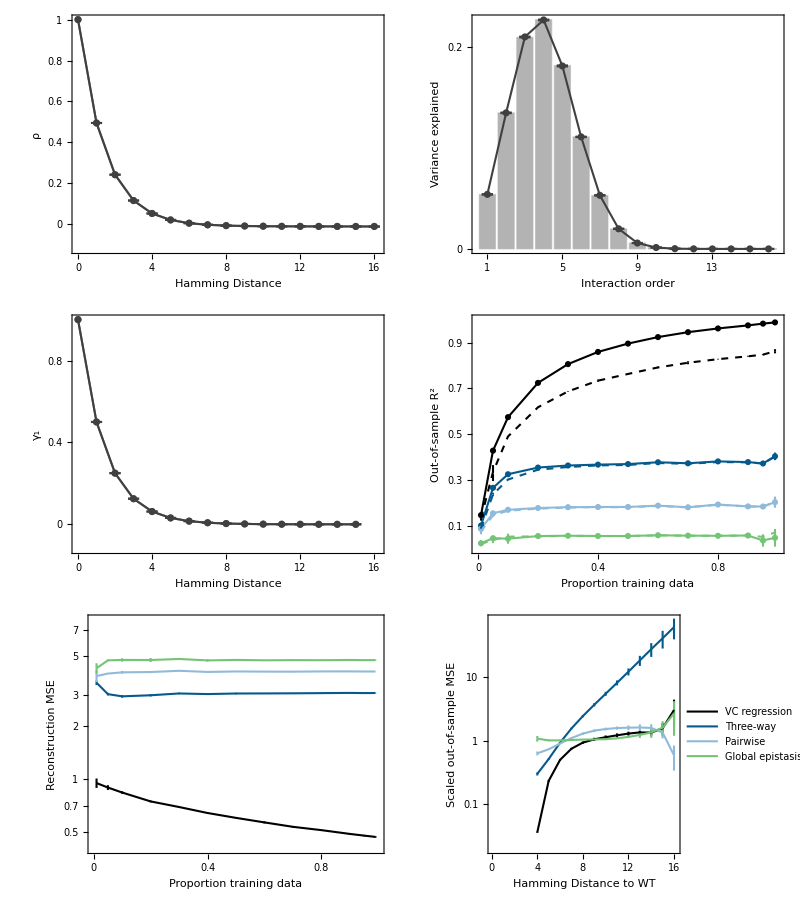

```mathematica
panels=Join[summaryfig3[PadLeft[lambdasAll[[i]],ls[[i]]+1],lambdaspos,vcsAll[[i]],  alphas[[i]], ls[[i]]], {MakeR2figure[results[[i]][[1]]],MSErecon[results[[i,2,2,1]],fl],MSEbyD[results[[i]][[2,3]],fls[[i]],trmutAll[[i]], alphas[[i]],ls[[i]], samplings[[i]]][[2]]}];
Grid[ArrayReshape[labelfigs[panels],{3,2}],Spacings->{1,.1}]
Export[StringJoin[figpath,"/Fig2.pdf"], %];
```

### Plot 6 x 6

```mathematica
results[[6,1]][[1]][[model]]=results[[5,1]][[1]][[model]][[{2,1,2}]];
results[[6,1]][[2,2]][[model]]=results[[5,1]][[2,2]][[model]][[{1,1,2}]];
```

```mathematica
plfontsize=36;
panellabs={Style[Text["α = 2, l = 16, dense interactions"],FontSize->plfontsize, FontFamily->"Helvetica"],
Style[Text["α = 2, l = 16, sparse interactions"],FontSize->plfontsize, FontFamily->"Helvetica"],
Style[Text["α = 4, l = 8, dense interactions"],FontSize->plfontsize, FontFamily->"Helvetica"],
Style[Text["α = 4, l = 8, sparse interactions"],FontSize->plfontsize, FontFamily->"Helvetica"],
Style[Text["α = 20, l = 4, dense interactions"],FontSize->plfontsize, FontFamily->"Helvetica"],
Style[Text["α = 20, l = 4, sparse interactions"],FontSize->plfontsize, FontFamily->"Helvetica"]};
```

```mathematica
numb[n_]:=Style[StringJoin[" ",ToString@n],FontSize->plfontsize, FontFamily->"Helvetica",FontWeight->"Bold"]
```

```mathematica
Needs["MaTeX`"]
altex=MaTeX["\\boldsymbol{\\alpha= }",FontSize->plfontsize];
ltex=MaTeX["\\boldsymbol{l= }",FontSize->plfontsize];
comma= Style[", ",FontSize->plfontsize, FontFamily->"Helvetica",FontWeight->"Bold"];
den=Style["dense interactions",FontSize->plfontsize, FontFamily->"Helvetica",FontWeight->"Bold"];
spr=Style["sparse interactions",FontSize->plfontsize, FontFamily->"Helvetica",FontWeight->"Bold"];
```

```mathematica
samps={den,spr,den,spr,den,spr};
```

```mathematica
panlabs=Table[Row[{altex, numb@alphas[[i]],comma,ltex,numb@ls[[i]], comma, samps[[i]]}],{i,6}];
```

```mathematica
Allpanels=Table[Make6P[i],{i,{3,1,5,4,2,6}}];
```

Import::nffil: File 4_8_DEN/out/posterior_lambdas.csv not found during Import.

Import::nffil: File 20_4_DEN/out/posterior_lambdas.csv not found during Import.

```mathematica
figAllpanels=Grid[ArrayReshape[Allpanels,{2,3}],Spacings->{7,2}];
```

```mathematica
Export[StringJoin[figpath,"/Supp_6x6panels.pdf"],figAllpanels];
```